```mathematica
Quit[];
```

# MGPT_qfunctions (August, 2018) compute q functions

Authors:

Mario Alberto Rodriguez-Meza (ININ, Mexico)
marioalberto.rodriguez@inin.gob.mx

Alejandro Aviles (Conacyt/ININ, Mexico)
alejandro.aviles.conacyt@inin.gob.mx, avilescervantes@gmail.com

References: 
For CLPT:                arXiv:1209.0780  (But we use the expansion of arXiv:1506.05264 )
For CLPT in MG:    arXiv:1705.10719, arXiv: 1809.xxxxx

If you use this code, please cite the reference arXiv: 1809.xxxxx. You may also want to cite the other references listed above.

RUN:  shift-enter on the biggest right bracket →
It runs in about 5-10 min

```mathematica
INPUTFILE="kfunctions_nb.dat"
OUTFILE="qfunctions_nb.dat"
```

kfunctionsN1_nb.dat

qfunctionsN1_nb.dat

## 1. Starting Mathematica

Initializing...

```mathematica
SetDirectory[NotebookDirectory[]];
FileNames[]
```

{kfunctionsN1_nb.dat,MGPT_CLPT.nb,MGPT_qfunctions.nb}

## 2. Definitions

```mathematica
pi=4. ArcTan[1];
pi2=pi*pi;
twopi2=2. pi2 ;
```

## 3. q Functions

Dependencies: sections 1 and 2 and Q and R k-functions and power spectrum in: “kfunctions” data file.

### Importing tables (PSL(k), Q(k) and R(k) functions)

```mathematica
QsRsTable=Import[INPUTFILE,"Data"];
```

```mathematica
QsRsTableRed=Drop[QsRsTable,2];
```

```mathematica
colk=Transpose[QsRsTableRed][[{1}]][[1]];
colPSL=Transpose[QsRsTableRed][[{18}]][[1]];colQ1=Transpose[QsRsTableRed][[{2}]][[1]];
colQI=Transpose[QsRsTableRed][[{12}]][[1]];
colQ2=Transpose[QsRsTableRed][[{3}]][[1]];
colQ5=Transpose[QsRsTableRed][[{5}]][[1]];
colQ8=Transpose[QsRsTableRed][[{7}]][[1]];
colR1=Transpose[QsRsTableRed][[{13}]][[1]];
colR2=Transpose[QsRsTableRed][[{14}]][[1]];
colRI=Transpose[QsRsTableRed][[{16}]][[1]];
colR1plus2=Transpose[QsRsTableRed][[{15}]][[1]];
```

```mathematica
PSLT=Table[{colk[[i]],colPSL[[i]]},{i,Length[colk]}];
PSL=Interpolation[PSLT]
Q1T=Table[{colk[[i]],colQ1[[i]]},{i,Length[colk]}];
Q1=Interpolation[Q1T];
QIT=Table[{colk[[i]],colQI[[i]]},{i,Length[colk]}];
QI=Interpolation[QIT];
Q2T=Table[{colk[[i]],colQ2[[i]]},{i,Length[colk]}];
Q2=Interpolation[Q2T];
Q5T=Table[{colk[[i]],colQ5[[i]]},{i,Length[colk]}];
Q5=Interpolation[Q5T];
Q8T=Table[{colk[[i]],colQ8[[i]]},{i,Length[colk]}];
Q8=Interpolation[Q8T];
R1T=Table[{colk[[i]],colR1[[i]]},{i,Length[colk]}];
R1=Interpolation[R1T];
R2T=Table[{colk[[i]],colR2[[i]]},{i,Length[colk]}];
R2=Interpolation[R2T];
RIT=Table[{colk[[i]],colRI[[i]]},{i,Length[colk]}];
RI=Interpolation[RIT];
R1plus2T=Table[{colk[[i]],colR1plus2[[i]]},{i,Length[colk]}];
R1plus2=Interpolation[R1plus2T];
```

InterpolatingFunction[{{0.0000109648, 301.995}}, <>]

```mathematica
kmaxQR=Max[QsRsTableRed[[All,1]]]
kminQR=Min[QsRsTableRed[[All,1]]]
```

301.995

0.0000109648

### Bessel functions

```mathematica
j0[x_]:=Sin[x]/x
j1[x_]:=Sin[x]/x^2-Cos[x]/x
j2[x_]:=(3/x^2-1)Sin[x]/x-(3 Cos[x])/x^2
j3[x_]:=(15/x^3-6/x)Sin[x]/x-(15/x^2-1)Cos[x]/x
```

### Create tables of k and q points

kT is used in all q functions except in χ_L (linear correlation function) and its derivatives

```mathematica
Nkpoints=1200;
kmin=kminQR;
(*kmax=20;*)
kmax=kmaxQR;
dk=(Log10[kmax]-Log10[kmin])/(Nkpoints);
kT=Table[10^(Log10[kmin]+ii*dk),{ii,0,Nkpoints}];
sizekT=Dimensions[kT][[1]];
Print["kT2 : sizekT=",sizekT,", kmin=",Min[kT],", k2max=",Max[kT]]
```

kT2 : sizekT=1201, kmin=0.0000109648, k2max=301.995

```mathematica
qmin=0.0001;
qmax=Min[300,1/kminQR];
Nqpoints=1200;
d=(Log10[qmax]-Log10[qmin])/(Nqpoints);
qT=Table[10^(Log10[qmin]+ii*d),{ii,0,Nqpoints}];
sizeqT=Dimensions[qT][[1]];
Print["qT : sizeqT=",sizeqT,", qmin=",Min[qT],", qmax=",Max[qT]]
```

qT : sizeqT=1201, qmin=0.0001, qmax=300.

### q functions (except linear correlation function and its derivatives)

#### Define kernels

```mathematica
tildeV[k_]:= -(3./35.)(QI[k]-3.Q2[k]+2. RI[k]-6.R2[k])
tildeT[k_]:=-(9./14.)  (QI[k]+2.Q2[k]+2. RI[k]+4.R2[k])
xL[k_,q_]:=PSL[k](1./3.-j1[k q]/(k q))
xloop[k_,q_]:=(9./98.Q1[k]+10./21. R1[k])(1./3.-j1[k q]/(k q))
yL[k_,q_]:=PSL[k] j2[k q]
yloop[k_,q_]:=(9./98.Q1[k]+10./21. R1[k])j2[k q]
x10[k_,q_]:=1./14.(2.RI[k]-2.R2[k]+3.RI[k] j0[k q]-3(RI[k]+2.R2[k]+2.R1plus2[k]+2.Q5[k])j1[k q]/(k q))
y10[k_,q_]:=-3./14.(RI[k]+2.R2[k]+2.R1plus2[k]+2.Q5[k])(j0[k q]-3 j1[k q]/(k q))
```

#### Integrate:

```mathematica
U10LT={};
U10loopT={};
U11T={};
U20T={};
XLT={};
XloopT={};
YLT={};
YloopT={};
X10T={};
Y10T={};
VT={};
TT={};

kmin=kT[[1]];
Do[
(*ta=AbsoluteTime[];*)
qi=qT[[qoutin]];

U10Lp=0  ;U10loopp=0  ;U11p=0  ;U20p=0  ;
U10LA=- kmin*(PSL[kmin])j1[kmin qi];
U10loopA=- kmin*(5./21.R1[kmin])j1[kmin qi];
U11A=- kmin*(6./7.R1plus2[kmin])j1[kmin qi];
U20A=- kmin*(3./7.Q8[kmin])j1[kmin qi];

XLp=0  ;Xloopp=0 ;YLp=0  ;Yloopp=0  ;X10p=0  ;Y10p=0  ;
XLA=xL[kmin,qi];
XloopA=xloop[kmin,qi];
YLA=yL[kmin,qi];
YloopA=yloop[kmin,qi];
X10A=x10[kmin,qi];
Y10A=y10[kmin,qi];

preVp=0  ;Tp=0  ;
preVA=tildeV[kmin]j1[kmin qi]/kmin;
TA= tildeT[kmin]j3[kmin qi]/kmin;



Do[
kk=kT[[kii]];
deltak=(kT[[kii]]-kT[[kii-1]]);

U10LB=- kk*(PSL[kk])j1[kk qi];
U10loopB=- kk*(5./21.R1[kk])j1[kk qi];
U11B=- kk*(6./7.R1plus2[kk])j1[kk qi];
U20B=- kk*(3./7.Q8[kk])j1[kk qi];
U10Lp=U10Lp+(U10LA+U10LB)/2*deltak;
U10LA=U10LB;
U10loopp=U10loopp+(U10loopA+U10loopB)/2*deltak;
U10loopA=U10loopB;
U11p=U11p+(U11A+U11B)/2*deltak;
U11A=U11B;
U20p=U20p+(U20A+U20B)/2*deltak;
U20A=U20B;

XLB=xL[kk,qi];
XloopB=xloop[kk,qi];
YLB=yL[kk,qi];
YloopB=yloop[kk,qi];
X10B=x10[kk,qi];
Y10B=y10[kk,qi];
XLp=XLp+(XLA+XLB)/2*deltak;
XLA=XLB;
Xloopp=Xloopp+(XloopA+XloopB)/2*deltak;
XloopA=XloopB;
YLp=YLp+(YLA+YLB)/2*deltak;
YLA=YLB;
Yloopp=Yloopp+(YloopA+YloopB)/2*deltak;
YloopA=YloopB;
X10p=X10p+(X10A+X10B)/2*deltak;
X10A=X10B;
Y10p=Y10p+(Y10A+Y10B)/2*deltak;
Y10A=Y10B;

preVB=tildeV[kk]j1[kk qi]/kk;
TB=tildeT[kk]j3[kk qi]/kk;
Tp=Tp+(TA+TB)/2*deltak;
TA=TB;
preVp=preVp+(preVA+preVB)/2*deltak;
preVA=preVB;

,{kii,2,sizekT}];

U10Lp=U10Lp/twopi2;
U10loopp=U10loopp/twopi2;
U11p=U11p/twopi2;
U20p=U20p/twopi2;
U10LT  =Append[U10LT,   {qi,U10Lp}];
U10loopT  =Append[U10loopT,   {qi,U10loopp}];
U11T  =Append[U11T,   {qi,U11p}];
U20T  =Append[U20T,   {qi,U20p}];


XLp=XLp/pi2;
YLp=YLp/pi2;
Xloopp=Xloopp/pi2;
Yloopp=Yloopp/pi2;
X10p=X10p/pi2;
Y10p=Y10p/pi2;
XLT  =Append[XLT,   {qi,XLp}];
XloopT  =Append[XloopT,   {qi,Xloopp}];
YLT  =Append[YLT,   {qi,YLp}];
YloopT  =Append[YloopT,   {qi,Yloopp}];
X10T  =Append[X10T,   {qi,X10p}];
Y10T  =Append[Y10T,   {qi,Y10p}];


Vp=preVp/pi2-1/5. Tp/pi2;
Tp=Tp/pi2;
If[qi<0.05,Vp=0,Vp=Vp];
If[qi<0.05,Tp=0,Tp=Tp];
VT  =Append[VT,   {qi,Vp}];
TT  =Append[TT,   {qi,Tp}];

(*Print[qoutin,": q=",qi, ":    U  = ",U10p, ",     time= ",AbsoluteTime[]-ta];*)
,{qoutin,1,sizeqT}]//AbsoluteTiming
```

{333.25868,Null}

### Linear Correlation Function and its derivatives

This is the Fourier Transform of PS. It should be computed with much more k points to avoid aliasing

```mathematica
Nkpoints2=12000;
k2min=kminQR;
k2max=20;
dk=(Log10[k2max]-Log10[k2min])/(Nkpoints2);
kT2=Table[10^(Log10[k2min]+ii*dk),{ii,0,Nkpoints2}];
Max[%]
Min[%%]
sizekT2=Dimensions[kT2][[1]]
```

20.

0.0000109648

12001

```mathematica
xiLT={};
LapxiLT={}; (*Laplacian of xi_L*)
nabla4xiLT={}; (* nabla4 xi_L*)
kmin=kT2[[1]]
Do[
ta=AbsoluteTime[];
qi=qT[[qoutin]];
xip=0  ;
xiA= kmin ^2PSL[kmin]j0[kmin qi];
Lapxip=0  ;
LapxiA= kmin ^4PSL[kmin]j0[kmin qi]Exp[-(kmin)^2];
nabla4xip=0  ;
nabla4xiA= kmin ^6PSL[kmin]j0[kmin qi]Exp[-(2*kmin)^2];
Do[
kk=kT2[[kii]];
xiB= kk ^2PSL[kk]j0[kk qi];
LapxiB= kk^2*xiB * Exp[-(kk )^2]; (* with antialising exponential*)
nabla4xiB= kk^4*xiB * Exp[-(2*kk )^2];(* with antialising exponential*)
deltak=(kT2[[kii]]-kT2[[kii-1]]);
xip=xip+(xiA+xiB)/2*deltak;
xiA=xiB;
Lapxip=Lapxip+(LapxiA+LapxiB)/2*deltak;
LapxiA=LapxiB;
nabla4xip=nabla4xip+(nabla4xiA+nabla4xiB)/2*deltak;
nabla4xiA=nabla4xiB;
,{kii,2,sizekT2}];
xip=xip/twopi2;
Lapxip=- Lapxip/twopi2;
nabla4xip=nabla4xip/twopi2;
xiLT  =Append[xiLT,   {qi,xip}];
LapxiLT  =Append[LapxiLT,   {qi,Lapxip}];
nabla4xiLT  =Append[nabla4xiLT,   {qi,nabla4xip}];
,{qoutin,1,sizeqT}]//AbsoluteTiming
```

0.0000109648

{285.77004,Null}

### Export files

```mathematica
qFunctionsT=Table[{XLT[[ii,1]],XLT[[ii,2]],YLT[[ii,2]],XloopT[[ii,2]],YloopT[[ii,2]],VT[[ii,2]],TT[[ii,2]],X10T[[ii,2]],Y10T[[ii,2]],U10LT[[ii,2]],U10loopT[[ii,2]],U11T[[ii,2]],U20T[[ii,2]],xiLT[[ii,2]],LapxiLT[[ii,2]],nabla4xiLT[[ii,2]] },{ii,1,Dimensions[XLT][[1]]}];
Dimensions[%]
Export[OUTFILE,qFunctionsT]
```

{1201,16}

qfunctionsN1_nb.dat

# PLOTS

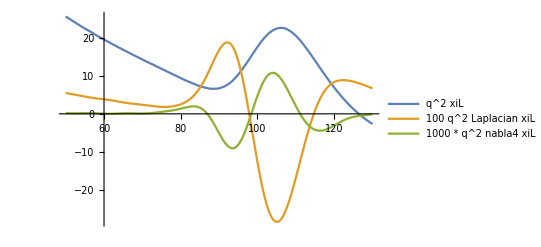

```mathematica
xiL=Interpolation[xiLT];
LapxiL=Interpolation[LapxiLT];
nabla4xiL=Interpolation[nabla4xiLT];
Plot[{r^2xiL[r],100r^2LapxiL[r],1000r^2nabla4xiL[r]},{r,50,130},PlotLegends->{"q^2 xiL ","100 q^2 Laplacian xiL","1000 * q^2 nabla4 xiL"}]
```

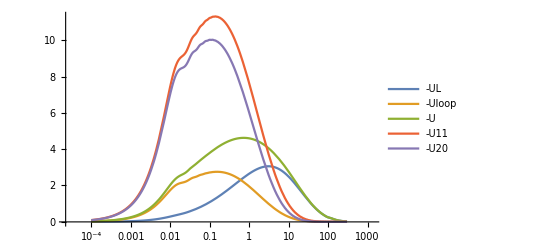

```mathematica
UL=Interpolation[U10LT];
Uloop=Interpolation[U10loopT];
U11=Interpolation[U11T];
U20=Interpolation[U20T];
LogLinearPlot[{-UL[q],-Uloop[q],-UL[q]-Uloop[q],-U11[q],-U20[q]},{q,0.0001,300},PlotRange->All,PlotLegends->{"-UL","-Uloop","-U","-U11","-U20"}]
```

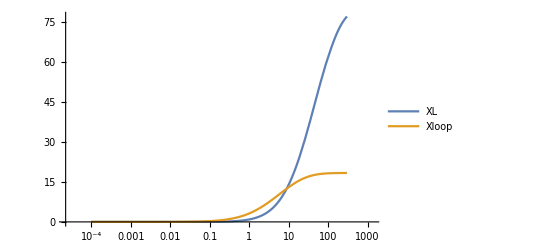

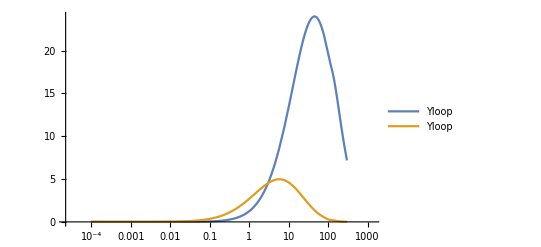

```mathematica
XL=Interpolation[XLT];
Xloop=Interpolation[XloopT];
YL=Interpolation[YLT];
Yloop=Interpolation[YloopT];
LogLinearPlot[{XL[q],Xloop[q]},{q,0.0001,300},PlotRange->All,PlotLegends->{"XL","Xloop"}]
LogLinearPlot[{YL[q],Yloop[q]},{q,0.0001,300},PlotRange->All,PlotLegends->{"Yloop","Yloop"}]
```

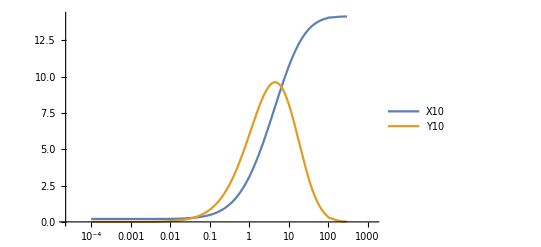

```mathematica
X10=Interpolation[X10T];
Y10=Interpolation[Y10T];
LogLinearPlot[{X10[q],Y10[q]},{q,0.0001,300},PlotLegends->{"X10","Y10"}]
```

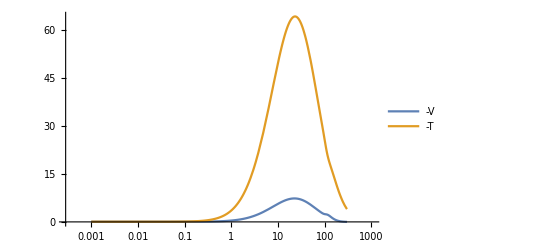

```mathematica
V=Interpolation[VT];
T=Interpolation[TT];
LogLinearPlot[{-V[q],-T[q]},{q,0.001,300},PlotLegends->{"-V","-T"},PlotRange->All]
```